```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY190/sec_int_data/778nm.dat"]
```

{{1.16196,-0.014799},{1.1485,-0.00844556},{1.13288,-0.0255948},{1.11879,-0.0892138},{1.10986,-0.211524},{1.10188,-0.341294},{1.0953,-0.447866},{1.09118,-0.450499},{1.08898,-0.346682},{1.08844,-0.162378},{1.08969,-0.0973923},{1.094,-0.0227774},{1.09832,-0.0145554},{1.10319,0.00299551},{1.11502,0.00149888},{1.13408,0.0198026},{1.14571,0.0201947},{1.16039,0.00588266},{1.17699,0.00558438},{1.19764,0.0119286},{1.21871,0.00329457},{1.24216,0.0018982},{1.26543,0.00548493},{1.29691,0.00508704},{1.32536,-0.00876833},{1.37118,-0.00636018},{1.45421,-0.0266726}}

-0.83015+0.639423 x

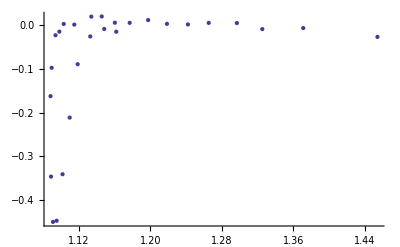

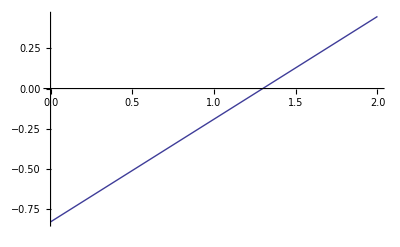

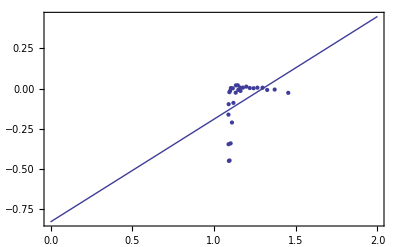

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```